# Chapter. Vector Calculus

##### Paul Abbott paul.c.abbott@uwa.edu.au

## Calculus of one variable

A quick review, with a slightly different view point:

### Taylor series

A function, f(x), is said to have n derivatives at x if

f(x+ϵ)==f(x)+ϵ f'(x)+1/2 ϵ^2 f''(x)+⋯+1/(n!)ϵ^n f^(n)(x)+𝒪(ϵ^(n+1))

The Taylor series exists up to the n^th order.

Use Series to compute the Taylor series of f(x+ϵ) about ϵ=0 to order 5:

```mathematica
Series[f[x+ϵ],{ϵ,0,4}]
```

f(x)+ϵ f'(x)+1/2 ϵ^2 f''(x)+1/6 ϵ^3 f^(3)(x)+1/24 ϵ^4 f^(4)(x)+O(ϵ^5)

The symbol 𝒪 is defined by

f(x)=𝒪(g(x))  if  ∃C∈ℝ such that  |f(x)|≤C|g(x)|  as x→0

Equations (Section.DisplayFormulaNumbered) and (Section.DisplayFormulaNumbered) can be used to define the n^th derivative.

This is known as the  notation and, when combined with the complementary little-o notation, can be used to rewrite most of analysis and calculus. These symbols are known as the  after the famous mathematical physicist , and were recently promoted in education by .

Adding the term O[ϵ]^(n+1) to a function computes its Taylor series to order n:

```mathematica
f[x+ϵ]+O[ϵ]^3
```

f(x)+ϵ f'(x)+1/2 ϵ^2 f''(x)+O(ϵ^3)

The Maclaurin series is just the Taylor series about the point 0:

```mathematica
f[x]+O[x]^4
```

f(0)+x f'(0)+1/2 x^2 f''(0)+1/6 f^(3)(0) x^3+O(x^4)

#### Example: sin(x)

Compute the Maclaurin series for sin(x) up to 11th order:

```mathematica
sin(x)+O[x]^12
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+O(x^12)

For a given function, Mathematica can also extract the general term:

```mathematica
SeriesCoefficient[sin(x),{x,0,n}]
```

Piecewise[{{(ⅈ ⅈ^n ((-1)^n-1))/(2 n!), n≥0}, {0, True}}]

```mathematica
Simplify[% x^n/.n->2 m+1,{m≥0,m∈Integers}]
```

((-1)^m x^(2 m+1))/((2 m+1)!)

The infinite sum converges:

```mathematica
∑_(m=0)^∞ ((-1)^m x^(2 m+1))/((2 m+1)!)
```

sin(x)

#### Example: sin(x)≃tan(x)≃x

Similarly we can expand tan(x):

```mathematica
tan(x)+O[x]^12
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835+(1382 x^11)/155925+O(x^12)

So we see that sin(x)=x+𝒪(x^3)=tan(x)  and for x “small enough” sin(x)≃tan(x)≃x.

```mathematica
sin(x)+O[x]^3==tan(x)+O[x]^3==x+O[x]^3
```

True

#### Formal Power Series

As an aside, the Taylor series for f(x+h) can be (formally) written as

f(x+h)==exp(h ∂/(∂x))f(x)

where we interpret the exponentiation of the differential operator h ⅆ/(ⅆ x)as a formal power series, ie

exp(a)==∑_(n=0)^∞ a^n/(n!) ⟹ exp(h ∂/(∂x))f(x)==∑_(n=0)^∞ h^n/(n!)∂^n/(∂x^n)f(x)==∑_(n=0)^∞ h^n/(n!)f^(n)(x)

This idea turns out to be useful, especially in group theory. The action of the differential operator ⅇ^(h ∂/(∂x)) on f(x) has the effect of translating the function to f(x+h).

### Tangent line

If we expand up to the linear term, we get the equation for the tangent line:

```mathematica
f(x)+O[x,a]^2
```

f(a)+(x-a) f'(a)+O((x-a)^2)

```mathematica
Normal[%]
```

(x-a) f'(a)+f(a)

Compare with y=c+m x; the slope is f'(a) and the y-intercept is f(a)-a f'(a).

#### Example

Display functions along with their tangent line. Colour the tangent line green if f''(a)<0, blue if f''(a)>0, and red if f''(a)≃0:

```mathematica
Manipulate[With[{δ=0.02},Plot[Evaluate@{f[x],Normal[f[x]+O[x,c]^2]/.c->a},{x,-9,9},AxesLabel->{"x",f[x]},PlotRange->1.5,PlotStyle->{Automatic,Which[f''[a]<-δ,Green,f''[a]>δ,Blue,Abs[f''[a]]<δ,Red]},Epilog->{Line[{{a,0},{a,f[a]}}],AbsolutePointSize[5],Point[{a,f[a]}]},ImageSize->300]],{{a,1.5},-8,8,Appearance->"Labeled"},{f,{x↦Sin[x],x↦Cos[x],x↦Exp[-(x/5)^2]Sin[2x]}},ControlPlacement->Top]
```

#### Example: Newton’s method

A nice application of the tangent line is  for finding the zeros of a function.

Solve for the x-intercept:

```mathematica
Solve[f[a]+(x-a)f'[a]==0,x]//Simplify
```

{{x→a-(f(a))/(f'(a))}}

Find the roots of the function f(x) by iteration.

#### Example: roots of a cubic

A cubic polynomial:

```mathematica
f[x_]:=-1+x/2+(5 x^2)/2+x^3
```

Plot the function:

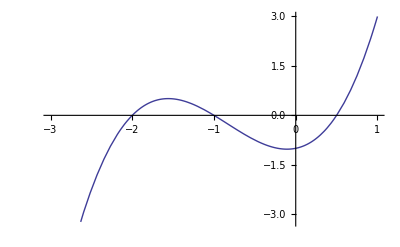

```mathematica
Plot[f[x],{x,-3,1}]
```

Use Solve to find all the solutons:

```mathematica
Solve[f[x]==0,x]
```

{{x→-2},{x→-1},{x→1/2}}

Find the roots of f(x) by iterating a↦a-(f(a))/(f'(a)) applied to an initial guess:

```mathematica
FixedPoint[a↦a-f[a]/f'[a],-0.7]
```

-1.

Note that the solution found depends upon the initial guess.

#### Example: Newton’s method explorer

```mathematica
Manipulate[newton[f,{x,-5,x0,5},n],
{f,{x^3-15x+4,x^2-2,Sin[x]},PopupMenu},
{{x0,-1.1,"x_0"},-4.5,4.5,Appearance->"Labeled"},
{{n,4},Range[5]},Initialization:>(newton[g_,{x_,x0_,c_,x1_},n_]:=Module[{f=Function[Evaluate@x,Evaluate@g],list},list=NestList[a↦a-f[a]/f'[a],c,n];Show[{Plot[f[x],{x,x0,x1},PlotRange-> All,Epilog->{{Red,Thickness[.002],Arrowheads[.03],Arrow[Most[Flatten[Map[x↦{{x,0},{x,f[x]}} ,list],1]]]},{PointSize[0.015],Point[{c,0}]}},ImageSize->{300,200}]}]]),SaveDefinitions->True]
```

### Maxima and Minima

The critical points of a curve f(x) are where f'(x)==0. In the neighbourhood of a critical point:

f(x+ϵ)==f(x)+1/2 ϵ^2 f''(x)+O(ϵ^3).

The critical points are

local maxima, for f''(x)<0

local minima, for f''(x)>0

points of inflection, for f''(x)==0

You learned these facts in (and should remember from) high-school calculus.

The point of these lectures is to examine what happens when x and ϵ are vectors in ℝ^n (we will mainly be concerned with n=2 and 3).

## Calculus of many variables

### Saddle point

Functions that depend on more than one variable have an extra type of critical point—the saddle point. A saddle point is a critical point that is not a local extremum.

#### Example: The canonical saddle: f(x,y)=x^2-y^2

This function is a parabola along the x-axis and an upside-down parabola along the y-axis. So, at (0,0) it has a local minima with respect to variations in x and a local maxima with respect to variations in y. The point (0,0) is called a saddle point.

```mathematica
Manipulate[Show[Plot3D[x^2-y^2,{x,-5,5},{y,-5,5},PlotRange->All,BoxRatios->1,AxesLabel->{"x","y","x^2-y^2"},Mesh->{5,5},MeshStyle->{Orange,Green}],ContourPlot3D[Evaluate[ToExpression@n],{x,-5,5},{y,-5,5},{z,-25,25},Mesh->None,ContourStyle->Directive[Yellow,Specularity[White,20],Opacity[0.4]]],Graphics3D[If[n=="z==0",{Line[{{-5,-5,0},{5,5,0}}],Line[{{-5,5,0},{5,-5,0}}]},{}]]],{{n,"y==0","Plane"},{"x==0","y==0","z==0"}}]
```

To proceed, we need to learn how to characterise surfaces near their critical points.

### Taylor series

We take a similar approach to above and examine the expansion of, eg, a function of two variables: f(x+δx)==f(x+δx,y+δy).

Initially just expand the first coordinate:

f(x+δx,y+δy)=f(x,y+δy)+δx∂_x f(x,y+δy)+1/2 δx^2∂_x^2 f(x,y+δy)+O(δx^3) .

Then substitute the expansion of the second coordinate:

f(x,y+δy)=f(x,y)+δy∂_y f(x,y)+1/2 δy^2∂_y^2 f(x,y)+O(δy^3),

to get

f(x+δx,y+δy)=f(x,y)+δx∂_x f(x,y)+δy∂_y f(x,y)
		     +1/2 δx^2∂_x^2 f(x,y)+δxδy∂_x ∂_y f(x,y)+1/2 δy^2∂_y^2 f(x,y)
		     +O(δx^3,δx^2 δy,δxδy^2,δy^3) .
=(1+δx∂_x +δy∂_y +1/2 δx^2∂_x^2 +δxδy∂_x ∂_y +1/2 δy^2∂_y^2 +… )f(x,y).

Now let's write x=(x,y), ∇=(∂_x,∂_y) and δx=(δx,δy) so that

δx∂_x +δy∂_y =δx·∇
δx^2∂_x^2 +2δxδy∂_x ∂_y +δy^2∂_y^2 =(δx·∇)^2

and we can write an expression that holds for all dimensions: ▽=(∂_x,∂_y,∂_z,...)

f(x+δx)==f(x)+δx·∇f(x)+1/2(δx·∇)^2 f(x)+O(δx^3)

The symbol ∇ is called Del or Nabla. In Mathematica it is entered as del. This symbol has no built-in meaning.

#### Example: Taylor series up to second order

Here is the Taylor series of f(x+δx)==f(x+δx,y+δy) including all terms of second order (along with some higher-order terms):

```mathematica
Series[f[x+δx,y+δy],{δx,0,2},{δy,0,2}]
```

(f(x,y)+δy f^(0,1)(x,y)+1/2 δy^2 f^(0,2)(x,y)+O(δy^3))+δx (f^(1,0)(x,y)+f^(1,1)(x,y) δy+1/2 f^(1,2)(x,y) δy^2+O(δy^3))+δx^2 (1/2 f^(2,0)(x,y)+1/2 f^(2,1)(x,y) δy+1/4 f^(2,2)(x,y) δy^2+O(δy^3))+O(δx^3)

The simplest way to organise multiple expansions is to include an additional (small) parameter ϵ. This groups together all terms of the same order:

```mathematica
f(x+ϵ δx,y+ϵ δy)+O[ϵ]^3
```

f(x,y)+ϵ (δx f^(1,0)(x,y)+δy f^(0,1)(x,y))+1/2 ϵ^2 (δx^2 f^(2,0)(x,y)+2 δx δy f^(1,1)(x,y)+δy^2 f^(0,2)(x,y))+O(ϵ^3)

#### Formal expansion

Generalising the one-dimensional formula, the Taylor series for f(x+δx) can be (formally) written as

f(x+δx)=exp(δx·∇)f(x)

This is a useful nmenonic.

### Directional derivative

If we truncate the Taylor series at first order,

f(x+δx)==f(x)+δx·∇f(x)

and set δx=ϵ û, where û is a unit vector, we get the definition of the directional derivative:

f'_(û) (x)==lim_(ϵ→0) (f(x+ϵ û)-f(x))/ϵ==û·∇f(x)

The directional derivative is the rate of change of f(x) in the direction û.

### ∇f or grad f

Now we can ask “in what direction does f(x) increase the fastest?"  The rate of change of f(x) in the direction û is

f'_(û) (x)==û·∇f(x)=cos(θ)|∇f(x)|

so it has a maximum when θ=0, i.e. when û points in the direction of ∇f(x).

The vector ∇f(x) points in the direction of greatest increase and its magnitude equals the rate of change of f in that direction. It is called the gradient of f and is often denoted grad(f). The gradient is the key to straightforward extension of some well-known equations that apply in one dimension. For example, the equation for heat conductivity

Φ==-kⅆT/(ⅆ x) ⟹Φ==-k∇T

where Φ is the heat flux across a surface and k is the thermal conductivity of that surface.

#### Example

Contours of equal temperature, T, with arrows representing the flow of heat -∇T for T(x)=α ⅇ^(-(x-a).(x-a))+β ⅇ^(-(x-b).(x-b)).

```mathematica
Manipulate[GraphicsGrid[{{Plot3D[temp[a,b,α,β][{x,y}],{x,-4,4},{y,-4,4},PlotRange->All,MeshFunctions->Function[{x,y,z},z]],Show[ContourPlot[temp[a,b,α,β][{x,y}],{x,-4,4},{y,-4,4},PlotRange->All],VectorPlot[Evaluate[-{D[temp[a,b,α,β][{x,y}], x],D[temp[a,b,α,β][{x,y}], y]}],{x,-4,4},{y,-4,4},VectorColorFunction->(Red&)],Frame->False,PlotRange->4]}},ImageSize->Large],{{a,{1,0}},{-3,-3},{3,3}},{{b,{-1,1/2}},{-3,-3},{3,3}},{{α,1},-1,1,Appearance->"Labeled",ControlPlacement->Top},{{β,1},-1,1,Appearance->"Labeled",ControlPlacement->Top},Initialization->(temp[a_,b_,c_,d_][x_]=c ⅇ^(-(x-a).(x-a))+d ⅇ^(-(x-b).(x-b))),SaveDefinitions->True,ControlPlacement->Left]
```

### Tangent plane and normal vector

As for the one-dimensional case, expanding some function f(x,y) near the point (x_0,y_0) to first order yields the equation for the tangent plane:

f(x,y)≃f(x_0,y_0)+(x-x_0) f^(1,0)(x_0,y_0)+(y-y_0)f^(0,1)(x_0,y_0)+…
⟹ f(x,y)≃f_lin(x,y)=(f_0-x_0 f_0^(1,0)-y_0 f_0^(0,1))+x f_0^(1,0)+y f_0^(0,1)+…

The tangent plane is described by the set of vectors (x-x_0,y-y_0,f_lin-f_0) with their origin at (x_0,y_0,f_0).

The normal is the vector (n_x,n_y,n_z) with origin (x_0,y_0,f_0) perpendicular to this plane. Writing δx=x-x_0 etc, we require

(n_x,n_y,n_z).(δx,δy,δx f_0^(1,0)+δy f_0^(0,1))==0  ∀δx,δy
⟹  (n_x,n_y,n_z)∝(f_0^(1,0),f_0^(0,1),-1)

Convention has the normal such that the surface curves away from it.

Note that (n_x,n_y,n_z)==∇g(x,y,z) where the equation g(x,y,z)==f(x,y)-z==0  defines the surface.

The tangent ‘plane’ can be defined in any dimension. The normal is special to three dimensions.

A critical point is where the tangent plane is horizontal, ie ∇f(x_0,y_0)==0  and so f(x,y)≃f_0-x_0 f_0^(1,0)-y_0 f_0^(0,1)==const.

#### Example

```mathematica
With[{dom=2,f=x↦Exp[-x.x],c=0.2},
Manipulate[Show[Plot3D[f[{x,y}],{x,-dom,dom},{y,-dom,dom},AxesLabel->{"x","y",f[{x,y}]},PlotRange->{0,1.5},Mesh->8,ImageSize->Medium,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.5]]],Plot3D[f[a]-a.{ Derivative[{1,0}][f][a], Derivative[{0,1}][f][a]}+{x,y}.{ Derivative[{1,0}][f][a], Derivative[{0,1}][f][a]},{x,a⟦1⟧-c,a⟦1⟧+c},{y,a⟦2⟧-c,a⟦2⟧+c},AxesLabel->{"x","sin(x)"},PlotRange->All,Mesh->None,PlotStyle->Red],Graphics3D[If[norm,Arrow[{Append[a,f[a]],Append[a,f[a]]-.4{Derivative[{1,0}][f][a],Derivative[{0,1}][f][a],-1}}],{Red,PointSize[Medium],Point[Append[a,f[a]]]}]]],{{a,{1,0}},{-dom,-dom},{dom,dom}},{{norm,True,"Normal"},{True,False}},ControlPlacement->Left]]
```

### The Hessian

In one-dimensional calculus, the sign of the second derivative tells us whether a critical point is a maxima or minima. In higher dimensions the same rôle is played by the Hessian.

Let's examine the second order term in the Taylor series expansion (Section.DisplayFormulaNumbered):

(δx·∇)^2 f(x)=δxᵀ·H·δx

where the  H is the matrix of second derivatives. The expression xᵀ·A·x is called a . In two-dimensions H has the form

H=((∂^2 f(x,y))/(∂x^2) | (∂^2 f(x,y))/(∂x ∂y)
(∂^2 f(x,y))/(∂y ∂x) | (∂^2 f(x,y))/(∂y^2))

Since partial derivatives commute, the Hessian is symmetric, H==Hᵀ.

Near a critical point, ∇f(x_0)=0, and (and dropping the δ's)

f(x_0+x)≃f(x_0)+0+1/2(x·∇)^2 f(x_0)==const+1/2 xᵀ·H·x

If we now choose (local) coordinates x so that the Hessian is diagonal, the surface near the critical point is like

f(x_0+x)≃const+1/2 λ_x x^2+1/2 λ_y y^2

Remember that a diagonalised matrix has the matrix eigenvalues along the diagonal.

#### Example

```mathematica
With[{d=10},
Manipulate[Row@{Plot3D[{x,y}.Q.{{λx,0},{0,λy}}.Inverse[Q].{x,y},{x,-d,d},{y,-d,d},Ticks->None,AxesLabel->{x,y},ImageSize->Medium,Mesh->False],"  ",Column[{Row[{TraditionalForm[{{Subscript[λ, x],Subscript[λ, y]}}ᵀ=={{λx,λy}}ᵀ],",     Q = ",MatrixForm@Q}],"",Row[{"2 f(x,y)==","(x,y)·Q^-1·(λ_x | 0
0 | λ_y)·Q·(x
y)"}],Row[{"         == ",Rationalize[#,.1]&@Chop@N[Expand[{x,y}.Inverse[Q].{{λx,0},{0,λy}}.Q.{x,y}],1]}]}]},{{λx,-1,"λ_x"},-1,1,.2},{{λy,-1,"λ_y"},-1,1,.2},{{Q,{{1,0},{0,1}},"Q"},{{{1,0},{0,1}}->"Identity",√2{{Cos[π/4],Sin[π/4]},{-Sin[π/4],Cos[π/4]}}->"Rotate π/4",{{.5,.5},{0,1}}->"x→(x+y)/2"},ControlType->PopupMenu}]]
```

See http://demonstrations.wolfram.com/EigenvaluesCurvatureAndQuadraticForms/.

### Summary

Taylor series in one variable about the point x_0:

f(x)==f(x_0)+(x-x_0) f'(x_0)+1/2(x-x_0)^2 f''(x_0)+⋯

If f'(x_0)==0 and f''(x_0)<0 then x_0 is a local maximum of f

If f'(x_0)==0 and f''(x_0)>0 then x_0 is a local minimum of f

If f'(x_0)==0 and f''(x_0)==0 then x_0 is an inflection point of f

Multi-variable Taylor series about the point x_0:

f(x)=f(x_0)+(x-x_0)· (∇f)(x_0)+1/2(x-x_0)^T·(∇(∇f))(x_0)·(x-x_0)+⋯

If (∇f)(x_0)=0 and the eigenvalues of the Hessian, ∇(∇f), evaluated at x_0, are all negative then x_0 is a local maximum of f.

If (∇f)(x_0)=0 and the eigenvalues of the Hessian, ∇(∇f), evaluated at x_0, are all positive then x_0 is a local minimum of f.

If the signs of the eigenvalues are mixed then x_0 is a saddle point.

## Vector Operators

In this section we examine the properties of ∇ in ℝ^3. This is useful because of the obvious connection to physics.

### Vector products

An ordinary vector v in ℝ^3 has three binary products:

Scalar multiplication: multiply by a scalar to yield a vector:

a∈ℝ,  v↦a v

Dot product: multiply by another vector, w to produce a scalar:

v·w=w·v=v_1 w_1+v_2 w_2+v_3 w_3=‖v‖‖w‖cos(θ_(v∡w))

Cross product (entered using cross, not *, which is Times): multiply by another vector, w to produce a vector:

v×w==-w×v==(v_2 w_3-v_3 w_2,v_3 w_1-v_1 w_3,v_1 w_2-v_2 w_1)

‖v×w‖=‖v‖‖w‖sin(θ_(v∡w))

#### Example

Define two vectors:

```mathematica
𝒱={Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]};
𝒲={Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]};
```

Dot product:

```mathematica
𝒱.𝒲
```

v_1 w_1+v_2 w_2+v_3 w_3

Crross product:

```mathematica
𝒱×𝒲
```

{v_2 w_3-v_3 w_2,v_3 w_1-v_1 w_3,v_1 w_2-v_2 w_1}

```mathematica
𝒱×𝒲==-𝒲×𝒱
```

True

#### Relation to determinant

Another way to compute the cross product uses the determinant:

```mathematica
basis={i,j,k};
```

```mathematica
Det[{basis,𝒱,𝒲}]
```

-i v_3 w_2+i v_2 w_3+j v_3 w_1-j v_1 w_3-k v_2 w_1+k v_1 w_2

```mathematica
Collect[Det[({{i, j, k}, {Subscript[v, 1], Subscript[v, 2], Subscript[v, 3]}, {Subscript[w, 1], Subscript[w, 2], Subscript[w, 3]}})],{i,j,k}]
```

i (v_2 w_3-v_3 w_2)+j (v_3 w_1-v_1 w_3)+k (v_1 w_2-v_2 w_1)

```mathematica
%/.{i->{1,0,0},j->{0,1,0},k->{0,0,1}}
```

{v_2 w_3-v_3 w_2,v_3 w_1-v_1 w_3,v_1 w_2-v_2 w_1}

Conversely, the 3×3 determinant can be computed using the cross product:

```mathematica
𝒰={Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]};
```

```mathematica
Det[({{Subscript[u, 1], Subscript[u, 2], Subscript[u, 3]}, {Subscript[v, 1], Subscript[v, 2], Subscript[v, 3]}, {Subscript[w, 1], Subscript[w, 2], Subscript[w, 3]}})]==𝒰.(𝒱×𝒲)//Expand
```

True

The determinant is invariant under cyclic rotation of rows ⟹𝒰.(𝒱×𝒲)==𝒱.(𝒲×𝒰)==𝒲.(𝒰×𝒱):

```mathematica
𝒰.𝒱×𝒲==𝒱.𝒲×𝒰==𝒲.𝒰×𝒱//Simplify
```

True

### Vector operators

Correspondingly there are three ways the vector operator ∇ can act:

On a scalar function f to yield a vector,  ∇f=grad(f)  (the gradient)

∇f==((∂f)/(∂x),(∂f)/(∂y),(∂f)/(∂z))

On a vector function f=(f_x,f_y,f_z)  via the dot product to yield a scalar, ∇·f=div(f) (the divergence)

∇·f==(∂f_x)/(∂x)+(∂f_y)/(∂y)+(∂f_z)/(∂z)

On a vector function f via the cross product to yield another vector,  ∇×f=curl(f)  (the curl or rotation)

∇×f==((∂f_z)/(∂y)-(∂f_y)/(∂z),(∂f_x)/(∂z)-(∂f_z)/(∂x),(∂f_y)/(∂x)-(∂f_x)/(∂y))==|i | j | k
∂_x  | ∂_y  | ∂_z 
f_x | f_y | f_z|

These operators can be accessed via the Vector Analysis Package, but it has a bit of a learning curve, so we can just define our own functions:

```mathematica
▽/:▽[f_]:={D[f, x],D[f, y],D[f, z]}
▽/:▽.{fx_,fy_,fz_}:=D[fx, x]+D[fy, y]+D[fz, z]
▽/:▽×{fx_,fy_,fz_}:={D[fz, y]-D[fy, z],D[fx, z]-D[fz, x],D[fy, x]-D[fx, y]}
```

The above functions only work if f=f(x,y,z).

Because Mathematica interprets ∇f as Del[f],  the above functions are defined with ▽=\[EmptyDownTriangle].

#### Examples

Define a set of three arbitrary vector functions (that is vectors for which each component is a function of x, y, and z) and two scalar functions,

```mathematica
𝒶={Subscript[a, 1][x,y,z],Subscript[a, 2][x,y,z],Subscript[a, 3][x,y,z]};
𝒷={Subscript[b, 1][x,y,z],Subscript[b, 2][x,y,z],Subscript[b, 3][x,y,z]};
𝒸={Subscript[c, 1][x,y,z],Subscript[c, 2][x,y,z],Subscript[c, 3][x,y,z]};
```

```mathematica
(𝒻=f[x,y,z];ℊ=g[x,y,z]);
```

Note that script letters (see the SpecialCharacters palette) have been use for the shorthand function name, e.g. 𝒻, and ordinary letters for the function itself. This prevents recursion; as a simple example, if you enter x=x+1, Mathematica will immediately start recursively applying this definition and go into a loop.

We will use the above definitions to confirm the standard vector identities:

#### Triple Products

```mathematica
𝒶.(𝒷×𝒸)==𝒷.(𝒸×𝒶)==𝒸.(𝒶×𝒷)//Expand
```

True

```mathematica
𝒶×(𝒷×𝒸)==𝒷 (𝒶.𝒸)-𝒸 (𝒶.𝒷)//Expand
```

True

#### Product (Leibniz) Rules

```mathematica
▽[𝒻 ℊ]==▽[𝒻]ℊ +𝒻 ▽[ℊ]
```

True

```mathematica
▽.(𝒻 𝒶)==▽[𝒻].𝒶 +(▽.𝒶)𝒻//Expand
```

True

```mathematica
▽×(𝒻 𝒶)==▽[𝒻]×𝒶 +(▽×𝒶)𝒻//Expand
```

True

```mathematica
▽[𝒶.𝒷]==𝒶 .▽[𝒷]+𝒷.▽[𝒶] -(▽×𝒶)×𝒷+𝒶×(▽×𝒷)//Simplify
```

True

```mathematica
▽.(𝒶×𝒷)==𝒷 .(▽×𝒶)-𝒶 .(▽×𝒷)//Expand
```

True

```mathematica
▽×(𝒶×𝒷)==𝒷 .▽[𝒶]-𝒶 .▽[𝒷]-(▽.𝒶)𝒷+𝒶(▽.𝒷)//Expand
```

### Second Derivatives

By applying ∇ twice one can construct five species of second derivatives.

#### 1. Divergence of gradient

The gradient ▽(𝒻) is a vector so we can take its divergence and curl:

```mathematica
▽·▽[𝒻]
```

f^(0,0,2)[x,y,z]+f^(0,2,0)[x,y,z]+f^(2,0,0)[x,y,z]

This is the Laplacian of 𝒻, often denoted ▽^2 𝒻≡Δ𝒻. The Laplacian of a scalar is a scalar.  
Occasionally one requires the Laplacian of a vector which is a vector, which is defined component-wise.

#### 2. Curl of gradient

```mathematica
▽×▽[𝒻]
```

{0,0,0}

The curl of a gradient is always identically zero.

#### 3. Gradient of divergence

The divergence ▽·𝒶 is a scalar—all we can do is take its gradient.

```mathematica
▽[▽·𝒶]
```

{(a_3)^(1,0,1)[x,y,z]+(a_2)^(1,1,0)[x,y,z]+(a_1)^(2,0,0)[x,y,z],(a_3)^(0,1,1)[x,y,z]+(a_2)^(0,2,0)[x,y,z]+(a_1)^(1,1,0)[x,y,z],(a_3)^(0,0,2)[x,y,z]+(a_2)^(0,1,1)[x,y,z]+(a_1)^(1,0,1)[x,y,z]}

This seldom occurs in physical applications and does not have a special name.

Note that ▽(▽·a)≠▽^2 a=(▽·▽)a.

#### 4. Divergence of curl

The curl ▽×𝒶 is a vector so we can take its divergence and curl.

```mathematica
▽.(▽×𝒶)
```

0

The divergence of a curl is always identically zero.

#### 5. Curl of curl

The vector identity ▽×(▽×𝒶)==▽(▽·𝒶)-▽·▽(𝒶) holds.

```mathematica
▽×(▽×𝒶)==▽[▽.𝒶]-▽.▽[𝒶]//Simplify
```

The curl of a curl gives nothing new. The first term on the right-hand side is the gradient of the divergence and the last is the Laplacian (of a vector). This identity is sometimes used to define the Laplacian of a vector,

▽^2 𝒶=▽(▽·𝒶)-▽×(▽×𝒶)

#### (bonus) Gradient of gradient

Extending the notation, we can compute the gradient of a gradient.

```mathematica
▽[▽[𝒻]]//TraditionalForm
```

(f^(2,0,0)(x,y,z) | f^(1,1,0)(x,y,z) | f^(1,0,1)(x,y,z)
f^(1,1,0)(x,y,z) | f^(0,2,0)(x,y,z) | f^(0,1,1)(x,y,z)
f^(1,0,1)(x,y,z) | f^(0,1,1)(x,y,z) | f^(0,0,2)(x,y,z))

This is the Hessian.

Note that the Laplacian is just the trace of the Hessian, and the gradient of the divergence is the row sum (a partial trace).

### Final notes

For notes on how to prove these identities by hand using index notation, see the Classical Mechanics section of Simon Tyler's Teaching page; or click .

A good reference is “Multivariable Calculus, Linear Algebra and Differential Equations” by Stanley Grossman.